# Discordia

# Calculo

```mathematica
ρ=1/4 (KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2]]+Sum[Subscript[x,i] KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]],{i,1,3}]+Sum[Subscript[y,i] KroneckerProduct[IdentityMatrix[2],PauliMatrix[i]],{i,1,3}]+Sum[Subscript[T,i,j] KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])
matrix={{a,0,0,0},{0,b,z,0},{0,z,c,0},{0,0,0,d}}
Solve[ρ==matrix&& Subscript[x,2]==0&&Subscript[y,2]==0&&Subscript[T,2,3]==0&&Subscript[T,3,2]==0&&Subscript[T,2,1]==0 &&Subscript[T,1,2]==0]
```

```mathematica
ρ=1/4 (f*KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2]]+Sum[Subscript[x,i] KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]],{i,1,3}]+Sum[Subscript[y,i] KroneckerProduct[IdentityMatrix[2],PauliMatrix[i]],{i,1,3}]+Sum[Subscript[T,i,j] KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])
matrix={{a,0,0,0},{0,b,z,0},{0,z,c,0},{0,0,0,d}}
Solve[ρ==matrix,{Subscript[x,1],Subscript[x,2],Subscript[x,3],Subscript[y,1],Subscript[y,2],Subscript[y,3],Subscript[T,1,1],Subscript[T,1,2],Subscript[T,1,3],Subscript[T,2,1],Subscript[T,2,2],Subscript[T,2,3],Subscript[T,3,1],Subscript[T,3,2],Subscript[T,3,3],f}]
```

# Estado-X

```mathematica
ρ=1/4 (f*KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2]]+Sum[Subscript[x,i] KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]],{i,1,3}]+Sum[Subscript[y,i] KroneckerProduct[IdentityMatrix[2],PauliMatrix[i]],{i,1,3}]+Sum[Subscript[T,i,j] KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])
matrix={{a,0,0,0},{0,b,I*z,0},{0,-I*z,c,0},{0,0,0,d}}
Solve[ρ==matrix,{Subscript[x,1],Subscript[x,2],Subscript[x,3],Subscript[y,1],Subscript[y,2],Subscript[y,3],Subscript[T,1,1],Subscript[T,1,2],Subscript[T,1,3],Subscript[T,2,1],Subscript[T,2,2],Subscript[T,2,3],Subscript[T,3,1],Subscript[T,3,2],Subscript[T,3,3],f}]
```

{{1/4 (f+x_3+y_3+T_(3,3)),1/4 (y_1-ⅈ y_2+T_(3,1)-ⅈ T_(3,2)),1/4 (x_1-ⅈ x_2+T_(1,3)-ⅈ T_(2,3)),1/4 (T_(1,1)-ⅈ T_(1,2)-ⅈ T_(2,1)-T_(2,2))},{1/4 (y_1+ⅈ y_2+T_(3,1)+ⅈ T_(3,2)),1/4 (f+x_3-y_3-T_(3,3)),1/4 (T_(1,1)+ⅈ T_(1,2)-ⅈ T_(2,1)+T_(2,2)),1/4 (x_1-ⅈ x_2-T_(1,3)+ⅈ T_(2,3))},{1/4 (x_1+ⅈ x_2+T_(1,3)+ⅈ T_(2,3)),1/4 (T_(1,1)-ⅈ T_(1,2)+ⅈ T_(2,1)+T_(2,2)),1/4 (f-x_3+y_3-T_(3,3)),1/4 (y_1-ⅈ y_2-T_(3,1)+ⅈ T_(3,2))},{1/4 (T_(1,1)+ⅈ T_(1,2)+ⅈ T_(2,1)-T_(2,2)),1/4 (x_1+ⅈ x_2-T_(1,3)-ⅈ T_(2,3)),1/4 (y_1+ⅈ y_2-T_(3,1)-ⅈ T_(3,2)),1/4 (f-x_3-y_3+T_(3,3))}}

{{a,0,0,0},{0,b,ⅈ z,0},{0,-ⅈ z,c,0},{0,0,0,d}}

{{x_1→0,x_2→0,x_3→a+b-c-d,y_1→0,y_2→0,y_3→a-b+c-d,T_(1,1)→0,T_(1,2)→2 z,T_(1,3)→0,T_(2,1)→-2 z,T_(2,2)→0,T_(2,3)→0,T_(3,1)→0,T_(3,2)→0,T_(3,3)→a-b-c+d,f→a+b+c+d}}

{{0,0,0},{0,16/((1/ⅇ+ⅇ)^2 (ⅇ^(-ea/2)+ⅇ^(ea/2))^2),0},{0,0,-4/((1/ⅇ+ⅇ)^2 (ⅇ^(-ea/2)+ⅇ^(ea/2))^2)+(ⅇ^(1/2 (-2-ea))/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2)))+ⅇ^((2-ea)/2)/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2)))-ⅇ^(1/2 (-2+ea))/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2)))-ⅇ^((2+ea)/2)/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2))))^2+(ⅇ^(1/2 (-2-ea))/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2)))-ⅇ^((2-ea)/2)/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2)))-ⅇ^(1/2 (-2+ea))/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2)))+ⅇ^((2+ea)/2)/((1/ⅇ+ⅇ) (ⅇ^(-ea/2)+ⅇ^(ea/2))))^2}}

{0,(16 ⅇ^(2+ea))/((1+ⅇ^2)^2 (1+ⅇ^ea)^2),(2 (1+ⅇ^4-2 ⅇ^ea+ⅇ^(2 ea)-2 ⅇ^(2+ea)-2 ⅇ^(4+ea)+ⅇ^(4+2 ea)))/((1+ⅇ^2)^2 (1+ⅇ^ea)^2)}

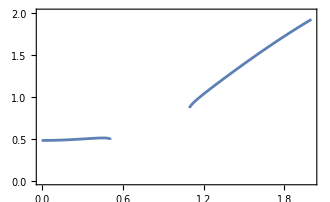

```mathematica
Za=Tr[MatrixExp[-ba*ea*PauliMatrix[3]/2]];
Zb=Tr[MatrixExp[-bb*eb*PauliMatrix[3]/2]];
a=Exp[(-ea*ba-eb*bb)/2]/(Za*Zb);
b=Exp[(-ea*ba+eb*bb)/2]/(Za*Zb);
c=Exp[(ea*ba-eb*bb)/2]/(Za*Zb);
d=Exp[(ea*ba+eb*bb)/2]/(Za*Zb);
z=1/(Za*Zb);
w=1/(Za*Zb);
Tij={{0,-2*(z+w),0},{0,-2*(w-z),-2*I*w},{0,0,a-b-c+d}};
xvec={{0,0,a+b-c-d}};
Traco[ea_]:=Simplify[Tr[(Transpose[Tij].Tij)+Transpose[xvec].xvec]]
K=(Transpose[Tij] . Tij) + Transpose[xvec] . xvec
eb=1;
ba=1;
bb=2;
Listaautovalores=Eigenvalues[K]
maxk[ea_]:=(1+ⅇ^4-2 ⅇ^ea+ⅇ^(2 ea)+2 ⅇ^(2+ea)-2 ⅇ^(4+ea)+ⅇ^(4+2 ea)+√((-1-ⅇ^4+2 ⅇ^ea-ⅇ^(2 ea)-2 ⅇ^(2+ea)+2 ⅇ^(4+ea)-ⅇ^(4+2 ea))^2-4 (4 ⅇ^(2+ea)+4 ⅇ^(6+ea)-8 ⅇ^(2+2 ea)-4 ⅇ^(4+2 ea)-8 ⅇ^(6+2 ea)+4 ⅇ^(2+3 ea)+4 ⅇ^(6+3 ea))))/((1+ⅇ^2)^2 (1+ⅇ^ea)^2);
Plot[Traco[ea]+maxk[ea],{ea,0,2},PlotRange->{0,2}]
```

# Estado-X Discordia

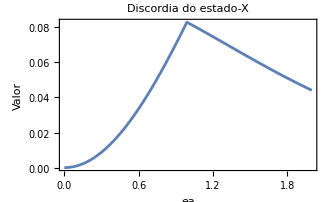

```mathematica
(*Limpa todas as definições anteriores para um início limpo*)ClearAll["Global`*"];

(* =====1. DEFINIÇÃO DE PARÂMETROS CONSTANTES=====*)
(*Colocamos os valores fixos no início.*)
ba=1;
bb=2;
eb=1;

(* =====2. DEFINIÇÃO DAS FUNÇÕES QUE DEPENDEM DE'ea'=====*)
(*Tudo o que muda com'ea',vira uma função de'ea'.*)

(*Otimização:Tr[MatrixExp[c*PauliMatrix[3]]] é 2*Cosh[c]*)
Za[ea_]:=2*Cosh[ba*ea/2];
Zb=2*Cosh[bb*eb/2]; (*Zb não depende de'ea',então é uma constante*)

a[ea_]:=Exp[(-ea*ba-eb*bb)/2]/(Za[ea]*Zb);
b[ea_]:=Exp[(-ea*ba+eb*bb)/2]/(Za[ea]*Zb);
c[ea_]:=Exp[(ea*ba-eb*bb)/2]/(Za[ea]*Zb);
d[ea_]:=Exp[(ea*ba+eb*bb)/2]/(Za[ea]*Zb);

z[ea_]:=1/(Za[ea]*Zb);
w[ea_]:=1/(Za[ea]*Zb);

Tij[ea_]:={{0,-2*(z[ea]+w[ea]),0},{0,-2*(w[ea]-z[ea]),0},{0,0,a[ea]-b[ea]-c[ea]+d[ea]}};
xvec[ea_]:={{0,0,a[ea]+b[ea]-c[ea]-d[ea]}};

(* =====3. CONSTRUÇÃO DA MATRIZ K COMO FUNÇÃO DE'ea'=====*)
(*K[ea_?NumericQ] garante que a função só será avaliada com valores numéricos,o que é perfeito para o Plot e muito mais eficiente.*)

K[ea_?NumericQ]:=(Transpose[Tij[ea]].Tij[ea])+(Transpose[xvec[ea]].xvec[ea]);


(* =====4. DEFINIÇÃO DAS FUNÇÕES PARA O GRÁFICO=====*)
(*Definimos o traço e o máximo autovalor como funções que calculam o valor numericamente para cada'ea'.Isso substitui sua fórmula'maxk'.*)

tracoK[ea_?NumericQ]:=Tr[K[ea]];
maxAutovalorK[ea_?NumericQ]:=Max[Eigenvalues[K[ea]]];


(* =====5. GERAÇÃO DO GRÁFICO FINAL=====*)
(*Agora,o Plot funciona corretamente chamando as funções bem definidas.*)
Plot[1/4*(tracoK[ea]-maxAutovalorK[ea]),{ea,0,2},AxesLabel->{"ea","Valor"},PlotLabel->"Discordia do estado-X"]
```

```mathematica
(*Calcula o valor da função em um ponto dentro do "corte"*)
valorNoCorte=tracoK[0.8]+maxAutovalorK[0.8]
```

Max::nord: Invalid comparison with {0.171709-0.0340432 ⅈ,0.171709+0.0340432 ⅈ,0.} attempted.

(0.343419+0. ⅈ)+Max[{0.171709-0.0340432 ⅈ,0.171709+0.0340432 ⅈ,0.}]

# Estado-X incompleto Discordia

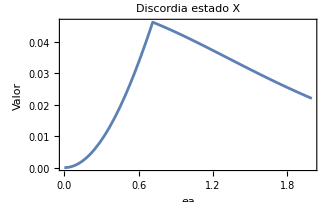

```mathematica
(*Limpa todas as definições anteriores para um início limpo*)ClearAll["Global`*"];

(* =====1. DEFINIÇÃO DE PARÂMETROS CONSTANTES=====*)
(*Colocamos os valores fixos no início.*)
ba=1;
bb=2;
eb=1;

(* =====2. DEFINIÇÃO DAS FUNÇÕES QUE DEPENDEM DE'ea'=====*)
(*Tudo o que muda com'ea',vira uma função de'ea'.*)

(*Otimização:Tr[MatrixExp[c*PauliMatrix[3]]] é 2*Cosh[c]*)
Za[ea_]:=2*Cosh[ba*ea/2];
Zb=2*Cosh[bb*eb/2]; (*Zb não depende de'ea',então é uma constante*)

a[ea_]:=Exp[(-ea*ba-eb*bb)/2]/(Za[ea]*Zb);
b[ea_]:=Exp[(-ea*ba+eb*bb)/2]/(Za[ea]*Zb);
c[ea_]:=Exp[(ea*ba-eb*bb)/2]/(Za[ea]*Zb);
d[ea_]:=Exp[(ea*ba+eb*bb)/2]/(Za[ea]*Zb);

z[ea_]:=1/(Za[ea]*Zb);
w[ea_]:=1/(Za[ea]*Zb);

Tij[ea_]:={{0,-2*z[ea],0},{0,2*z[ea],0},{0,0,a[ea]-b[ea]-c[ea]+d[ea]}};
xvec[ea_]:={{0,0,a[ea]+b[ea]-c[ea]-d[ea]}};

(* =====3. CONSTRUÇÃO DA MATRIZ K COMO FUNÇÃO DE'ea'=====*)
(*K[ea_?NumericQ] garante que a função só será avaliada com valores numéricos,o que é perfeito para o Plot e muito mais eficiente.*)

K[ea_?NumericQ]:=(Transpose[Tij[ea]].Tij[ea])+(Transpose[xvec[ea]].xvec[ea]);


(* =====4. DEFINIÇÃO DAS FUNÇÕES PARA O GRÁFICO=====*)
(*Definimos o traço e o máximo autovalor como funções que calculam o valor numericamente para cada'ea'.Isso substitui sua fórmula'maxk'.*)

tracoK[ea_?NumericQ]:=Tr[K[ea]];
maxAutovalorK[ea_?NumericQ]:=Max[Eigenvalues[K[ea]]];


(* =====5. GERAÇÃO DO GRÁFICO FINAL=====*)
(*Agora,o Plot funciona corretamente chamando as funções bem definidas.*)
Plot[1/4*(tracoK[ea]-maxAutovalorK[ea]),{ea,0,2},AxesLabel->{"ea","Valor"},PlotLabel->"Discordia estado X"]
```